In this file we will show the difference in quantum computing vs classic methods.

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

```mathematica
(* use TruthTable generator to create random function f(x) that is either Balanced or Constant; hopefully will work for both Quantum and Classical *)
makeTruthTable[n_Integer]:= Module[{type,bits},
type=RandomChoice[{"Constant","Balanced"}];
bits=If[type==="Constant",
(* All 0s or All 1s *)
If[RandomInteger[]==0,
ConstantArray[0,2^n],ConstantArray[1,2^n]],
(* Shuffle equal number of 0s and 1s *)
RandomSample[Join[ConstantArray[0,2^(n-1)],ConstantArray[1,2^(n-1)]]]];
<|"Bits"->bits,"Type"->type|>];
```

## Quantum Implementation:

```mathematica
(*Oracle Operator Generator*)makeOracleOperator[truthTable_List]:=Module[{n,perm,x,y,newY,dim,matrixRules,matrix},
n=Log2[Length[truthTable]];
(* Calculate the Permutation List *)
perm=Table[With[{val=i-1},
(*Target qubit is LSB*)
y=Mod[val,2];
x=Quotient[val,2];
newY=BitXor[y,truthTable[[x+1]]];
(x*2+newY)+1],
{i,1,2^(n+1)}];
dim=2^(n+1);
matrixRules=Table[{perm[[col]],col}->1,{col,1,dim}];
matrix=SparseArray[matrixRules,{dim,dim}];
(* Create the Operator from the Matrix *)
QuantumOperator[matrix,Range[n+1]]]
```

```mathematica
(*CONFIG->SELECT NUMBER OF INPUT QUBITS (n), starts to break down at 6-7 qubits (127 bit maximum, as qubits will to 2^(n-1)) *)
n = 6;
(* 'secret' oracle generation *)
oracleData = makeTruthTable[n];
(* for testing/ sanity, having it tell us hidden function type *)
Print["Actual Hidden Function Type:", oracleData["Type"]];
oracleOp = makeOracleOperator[oracleData["Bits"]];
```

Actual Hidden Function Type:Balanced

```mathematica
(* Actual Deutsch-Jozsa algorithm *)
(* should have n qubits om |0>, and last in |1> *)
(*CONFIG-> SELECT NUMBER OF INPUT QUBITS (n)*)
n = 6; 
initialState = QuantumTensorProduct[
QuantumState[{"Register", n}],
QuantumState[{1}, 2]];
(* gate definitions -> Circuit building *)
djCircuit = QuantumCircuitOperator[{
(* apply Hadamard Gate to each qubit (all inputs plus helper qubit) *)
QuantumOperator["H", Range[n + 1]],
(* situation custom oracle *)
oracleOp,
(* additional Hadamard Gate for input qubits only *)
QuantumOperator["H", Range[n]],
(* take measurements of input qubits *)
QuantumMeasurementOperator[Range[n]]}];
```

```mathematica
(* simulation (apply circuit to an initial state) *)
result = djCircuit[initialState];
```

```mathematica
(* results *)
Module[{probs,zeroStateKey,probZero,outcomeType},
probs=result["Probabilities"];
(* Identify the'All Zeros' key based on what the framework returned *)(* Sometimes it returns {0,0,0},sometimes "000", idk why, couldn't find in documentation *)zeroStateKey=If[KeyExistsQ[probs,ConstantArray[0,n]],
ConstantArray[0,n],(*Key is a list {0,0,0}*)
StringJoin[ConstantArray["0",n]] (*Key might be string "000" ugh*)];
(* Safely get the probability of the zero state (default to 0 if missing)*)
probZero=Lookup[probs,zeroStateKey,0];
Print["Measured Probability of |0...0>: ",probZero];
(* Determine Outcome*)If[probZero>0.99,outcomeType="CONSTANT",outcomeType="BALANCED"];
Print["Algorithm Conclusion: ",outcomeType];
(* Verify against the hidden Oracle Type*)Print["Verification: ",If[ToUpperCase[outcomeType]===ToUpperCase[oracleData["Type"]],"SUCCESS","FAILURE (Mismatch)"]];]
```

## Classical implementation

```mathematica
(*This function takes the list of bits returned from the makeTruthTable function, and iterates throught the list determining whether there are equal numbers of 0s and 1s, or if the list is all 0s or 1s *)
balancedorconstant[list_]:=Module[{count1,count0,iter},
count1=0;
count0=0;
iter=1;
Do[Which[list[iter]==1,count1 ++,list[iter]==0,count0 ++];iter++,Length[list]];
Which[count1-count0==0,Print["Balanced"],count0==0||count1==0,Print["Constant"]]
]
```

```mathematica
AbsoluteTiming[balancedorconstant[makeTruthTable[2][[1]]]]
```

Balanced

{0.0002728,Null}

```mathematica
balancedorconstant[makeTruthTable[4][[1]]]
```

Balanced

```mathematica
balancedorconstant[makeTruthTable[20][[1]]]//AbsoluteTiming
```

Balanced

{1.16438,Null}

```mathematica
balancedorconstant[makeTruthTable[25][[1]]]//AbsoluteTiming
```

Balanced

{32.5935,Null}

```mathematica
makeTruthTable[25][[1]];//AbsoluteTiming
```

{1.90126,Null}

```mathematica
balancedorconstantp[list_]:=Module[{count1,count0,iter},
count1=0;
count0=0;
iter=1;
Do[Which[list[iter]==1,count1 ++,list[iter]==0,count0 ++];iter++,Length[list]];
Which[count1-count0==0,"Balanced",count0==0||count1==0,"Constant"];
]
```

```mathematica
balancedorconstantp[makeTruthTable[1]]//AbsoluteTiming
```

{0.0001259,Null}

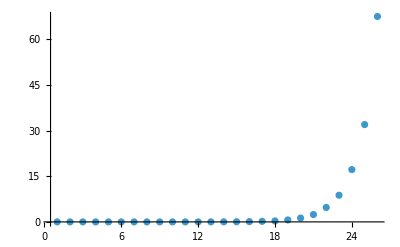

-1.61264+3.37348×10^-10 ⅇ^x+0.206903 x

```mathematica
graphinglist={};
Do[AppendTo[graphinglist,{i,AbsoluteTiming[balancedorconstantp[makeTruthTable[i][[1]]]][[1]]}],{i,1,26}];
ListPlot[graphinglist,PlotRange->All]
Fit[graphinglist,{1,x,E^x},x]
```